### Settings

```mathematica
d=4;
a=8;
delta = 0.000001;
rMax=20; 
Z = N[1/(2*Pi*d)];
```

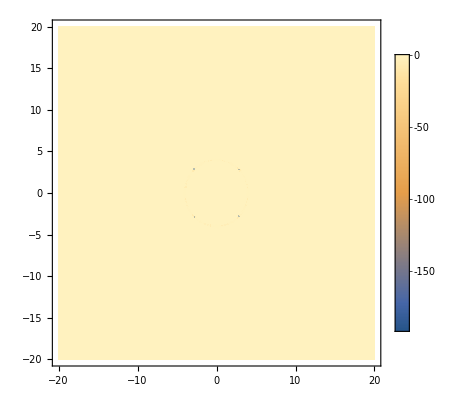

```mathematica
V[r_, θ_] := (-Z)/(Abs[r-0*d*Cos[θ]^2 -d]+delta) *Exp[-Abs[r-0*d*Cos[θ]^2 -d]/a] + 2; 
DensityPlot[V[r ,θ]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax}, (*PlotTheme->"Minimal"*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
(*Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];*)
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/2)* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r,θ]*R2D[r,θ],
DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},10, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{1.90832,1.95301,1.95301,2.00775,2.01089,2.01397,2.0248,2.02959,2.03427,2.03554}

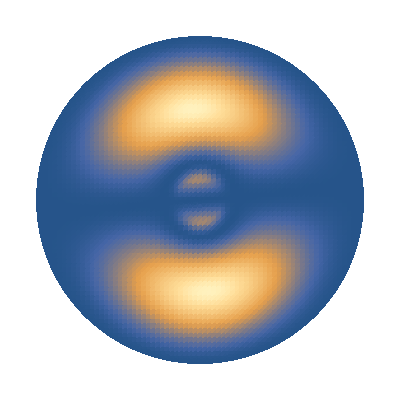

```mathematica
F1 =Part[Re[egnVec],Part[ord,5]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal", PlotPoints->100,PlotRange->All  (*PlotLegends->Automatic*)];
Show[{%,%%}]
Export[NotebookDirectory[]<>"5.png",%,ImageResolution->100];
```